# Process: u d̄ ->γ W^+

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Quit[]
```

```mathematica
process={F[3,{1}], -F[4,{1}]} -> {V[1], -V[3]}
```

{F[3,{1}],-F[4,{1}]}→{V[1],-V[3]}

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams



```mathematica
top=CreateTopologies[0,2->2];
Paint[top];
```

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 2 Generic, 2 Classes, 2 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

in total: 4 Generic, 4 Classes, 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

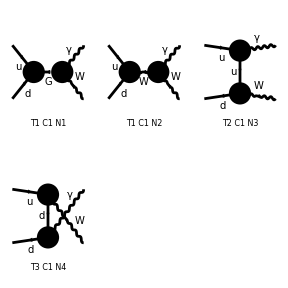

```mathematica
ins=InsertFields[tmp, process,InsertionLevel->Particles];
Paint[ins, PaintLevel->{Classes}];
```

```mathematica
amp=CreateFeynAmp[ins]
```

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 2 Generic, 2 Classes, 2 Particles amplitudes

> Top. 2: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 3: 1 Generic, 1 Classes, 1 Particles amplitudes

in total: 4 Generic, 4 Classes, 4 Particles amplitudes

FeynAmpList[Process→{{F[3,{1,Col1}],p1,MU,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[4,{1,Col2}],p2,MD,{Charge/3,-(2 ColorCharge)/(√3)}}}→{{V[1],k1,0,{}},{-V[3],k2,MW,Charge}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Generic,Classes,Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1],Integral[],RelativeCF v̄[p2,Mass[F[4,{1,Col2}]]].(om_- G_FFS^(0)[om_-]+om_+ G_FFS^(0)[om_+]).u[p1,Mass[F[3,{1,Col1}]]] g[Lor1,Lor2] 1/((k1+k2)^2-Mass[S[Gen5],Internal]^2) ep^*[V[1],k1,Lor1] ep^*[V[3],k2,Lor2] G_SVV^(0)[g[KI1[2],KI1[3]]],{Mass[F[3,{1,Col1}]],Mass[F[4,{1,Col2}]],Mass[S[Gen5],Internal],G_FFS^(0)[om_-],G_FFS^(0)[om_+],G_SVV^(0)[g[KI1[2],KI1[3]]],RelativeCF}→Insertions[Classes][{MU,MD,MW,-(ⅈ EL MD CKMC[1,1] IndexDelta[Col1,Col2])/(√2 MW SW),(ⅈ EL MU CKMC[1,1] IndexDelta[Col1,Col2])/(√2 MW SW),-ⅈ EL MW,SumOver[Col1,3,External] SumOver[Col2,3,External]}→Insertions[Particles][{MU,MD,MW,-(ⅈ EL MD CKMC[1,1] IndexDelta[Col1,Col2])/(√2 MW SW),(ⅈ EL MU CKMC[1,1] IndexDelta[Col1,Col2])/(√2 MW SW),-ⅈ EL MW,SumOver[Col1,3,External] SumOver[Col2,3,External]}]]],FeynAmp[GraphID[Topology==1,Generic==2],Integral[],-RelativeCF v̄[p2,Mass[F[4,{1,Col2}]]].(ga[Lor3].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor3].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).u[p1,Mass[F[3,{1,Col1}]]] ((k1-k2)[Lor4] g[Lor1,Lor2]+(-2 (k1)-k2)[Lor2] g[Lor1,Lor4]+(k1+2 (k2))[Lor1] g[Lor2,Lor4]) g[Lor3,Lor4] 1/((k1+k2)^2-Mass[V[Gen5],Internal]^2) ep^*[V[1],k1,Lor1] ep^*[V[3],k2,Lor2] G_VVV^(0)[(-Mom[1]+Mom[2])[KI1[3]] g[KI1[1],KI1[2]]+(Mom[1]-Mom[3])[KI1[2]] g[KI1[1],KI1[3]]+(-Mom[2]+Mom[3])[KI1[1]] g[KI1[2],KI1[3]]],{Mass[F[3,{1,Col1}]],Mass[F[4,{1,Col2}]],Mass[V[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_VVV^(0)[(-Mom[1]+Mom[2])[KI1[3]] g[KI1[1],KI1[2]]+(Mom[1]-Mom[3])[KI1[2]] g[KI1[1],KI1[3]]+(-Mom[2]+Mom[3])[KI1[1]] g[KI1[2],KI1[3]]],RelativeCF}→Insertions[Classes][{MU,MD,MW,(ⅈ EL CKMC[1,1] IndexDelta[Col1,Col2])/(√2 SW),0,ⅈ EL,SumOver[Col1,3,External] SumOver[Col2,3,External]}→Insertions[Particles][{MU,MD,MW,(ⅈ EL CKMC[1,1] IndexDelta[Col1,Col2])/(√2 SW),0,ⅈ EL,SumOver[Col1,3,External] SumOver[Col2,3,External]}]]],FeynAmp[GraphID[Topology==2,Generic==1],Integral[],RelativeCF v̄[p2,Mass[F[4,{1,Col2}]]].(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).(gs[-(p2)+k2]+Mass[F[Gen5],Internal]).(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).u[p1,Mass[F[3,{1,Col1}]]] 1/((p2-k2)^2-Mass[F[Gen5],Internal]^2) ep^*[V[1],k1,Lor1] ep^*[V[3],k2,Lor2],{Mass[F[3,{1,Col1}]],Mass[F[4,{1,Col2}]],Mass[F[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{MU,MD,MU,-(2 ⅈ EL)/3,-(2 ⅈ EL)/3,(ⅈ EL CKMC[1,1] IndexDelta[Col1,Col2])/(√2 SW),0,SumOver[Col1,3,External] SumOver[Col2,3,External]}→Insertions[Particles][{MU,MD,MU,-(2 ⅈ EL)/3,-(2 ⅈ EL)/3,(ⅈ EL CKMC[1,1] IndexDelta[Col1,Col2])/(√2 SW),0,SumOver[Col1,3,External] SumOver[Col2,3,External]}]]],FeynAmp[GraphID[Topology==3,Generic==1],Integral[],RelativeCF v̄[p2,Mass[F[4,{1,Col2}]]].(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).(gs[-(p2)+k1]+Mass[F[Gen5],Internal]).(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).u[p1,Mass[F[3,{1,Col1}]]] 1/((p2-k1)^2-Mass[F[Gen5],Internal]^2) ep^*[V[1],k1,Lor1] ep^*[V[3],k2,Lor2],{Mass[F[3,{1,Col1}]],Mass[F[4,{1,Col2}]],Mass[F[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{MU,MD,MD,(ⅈ EL CKMC[1,1])/(√2 SW),0,1/3 ⅈ EL IndexDelta[Col1,Col2],1/3 ⅈ EL IndexDelta[Col1,Col2],SumOver[Col1,3,External] SumOver[Col2,3,External]}→Insertions[Particles][{MU,MD,MD,(ⅈ EL CKMC[1,1])/(√2 SW),0,1/3 ⅈ EL IndexDelta[Col1,Col2],1/3 ⅈ EL IndexDelta[Col1,Col2],SumOver[Col1,3,External] SumOver[Col2,3,External]}]]]]

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{F[3,{1,Col1}],k[1],MU,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[4,{1,Col2}],k[2],MD,{Charge/3,-(2 ColorCharge)/(√3)}}}→{{V[1],k[3],0,{}},{-V[3],k[4],MW,Charge}}][-1/SW √2 Alfa π CKMC[1,1] (4 Sub4 Den[S,MW2]+4/3 Sub3 Den[T,MU2]-2/3 (F18-2 F15 Pair2+2 F16 Pair5) Den[U,MD2]) Mat[SUN1]]